```mathematica
SetDirectory["C:\\Users\\fareg\\Downloads\\hzgamma\\HtohZgammadiagram"]
If[$FrontEnd==Null, $FeynCalcStartupMessages=False;
	Print[description];];
If[$Notebooks == False, $FeynCalcStartupMessages = False];
$LoadFeynArts = True;
$LoadAddOns={"FeynHelpers"};
<<FeynCalc`;
$FAVerbose=0;
```

```mathematica
(*self energy Higgs*)
TwoPointsDiagrams = DiagramExtract[diagrams, TwoPoints];
SelfH = DiagramExtract[TwoPointsDiagrams, {1}];
```

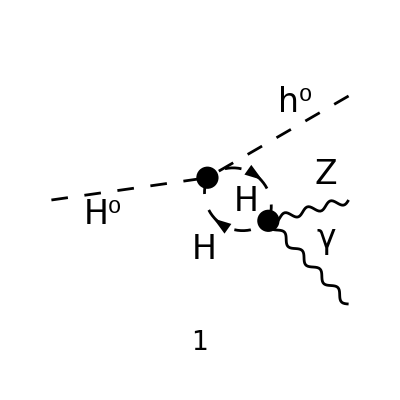

```mathematica
Paint[SelfH, Numbering->Simple, SheetHeader->None, ColumnsXRows->{1,1}];
```

```mathematica
Clear[ampsSelf]
ampsSelf = CreateFeynAmp[SelfH, Truncated->True, GaugeRules->{_FAGaugeXi->1}];
ampsSelf = FCFAConvert[ampsSelf, IncomingMomenta->{q}, OutgoingMomenta->{k1, k2, k3},
LoopMomenta-> {l},  ChangeDimension->D, UndoChiralSplittings->True, DropSumOver->True , TransversePolarizationVectors->{k1, k2}, List->True, 
SMP->True, LorentzIndexNames->{μ, ν, ρ, σ, δ, λ}, SUNIndexNames->{a,b,c,d,f,e,g,h},SUNFIndexNames-> {w,v,z,x,m,n,q,r}
]/.ConventionNotation//Contract//FCTraceFactor//Simplify
```

{(ⅈ g^μν g_(H H H0 h0) g_(H H Z γ))/(16 π^4 (l^2-m_Hp^2).((k2+k3-l)^2-m_Hp^2))}

```mathematica
F1self = P1[μ,ν]ampsSelf // Contract//Expand
F2self = P2[μ,ν] ampsSelf // Contract//Expand
F3self = P3[μ,ν] ampsSelf // Contract//Expand
```

{(ⅈ (k1·k3) g_(H H H0 h0) g_(H H Z γ))/(16 π^4 (l^2-m_Hp^2).((k2+k3-l)^2-m_Hp^2))-(ⅈ D (k1·k3) g_(H H H0 h0) g_(H H Z γ))/(16 π^4 (l^2-m_Hp^2).((k2+k3-l)^2-m_Hp^2))}

{(ⅈ (k2·k3) g_(H H H0 h0) g_(H H Z γ))/(16 π^4 (l^2-m_Hp^2).((k2+k3-l)^2-m_Hp^2))-(ⅈ D (k2·k3) g_(H H H0 h0) g_(H H Z γ))/(16 π^4 (l^2-m_Hp^2).((k2+k3-l)^2-m_Hp^2))}

{(ⅈ k1^2 g_(H H H0 h0) g_(H H Z γ))/(16 π^4 (l^2-m_Hp^2).((k2+k3-l)^2-m_Hp^2))+(ⅈ (k1·k2) (k1·k3) g_(H H H0 h0) g_(H H Z γ))/(16 π^4 (k2·k3) (l^2-m_Hp^2).((k2+k3-l)^2-m_Hp^2))}

```mathematica
f1selfreduced =F1self/.squareloopterms/.looplineardependences;
f2selfreduced = F2self/.squareloopterms/.looplineardependences;
f3selfreduced = F3self/.squareloopterms/.looplineardependences;
```

```mathematica
f1selfres = f1selfreduced//TID[#, l, ToPaVe->True]&//Simplify;
f2selfres = f2selfreduced// TID[#, l, ToPaVe->True]&//Simplify;
f3selfres = f3selfreduced// TID[#, l, ToPaVe->True]& //Simplify;
```

```mathematica
f1self =  f1selfres/.Kinematics/.InvariantKinematics;
f2self =  f2selfres/.Kinematics/.InvariantKinematics;
f3self =  f3selfres/.Kinematics/.InvariantKinematics;
```

```mathematica
f1Hself = Total[f1self]//Simplify
f2Hself = Total[f2self]//Simplify
f3Hself = Total[f3self]//Simplify
```

((D-1) (q_13-m_h0^2) g_(H H H0 h0) g_(H H Z γ) B_0(-m_Z^2+q_23,m_Hp^2,m_Hp^2))/(32 π^2)

-((D-1) g_(H H H0 h0) g_(H H Z γ) (m_h0^2+m_Z^2-q_23) B_0(-m_Z^2+q_23,m_Hp^2,m_Hp^2))/(32 π^2)

-(g_(H H H0 h0) g_(H H Z γ) (m_h0^2 (m_Z^2+q_12)+(q_13-2 q_23) m_Z^2+2 m_Z^4-q_12 q_13) B_0(-m_Z^2+q_23,m_Hp^2,m_Hp^2))/(32 π^2 (m_h0^2+m_Z^2-q_23))

```mathematica
Clear[F1self, F2self, F3self, f1selfreduced, f2selfreduced, f3selfreduced, f1selfres, f2selfres, f3selfres, f1self, f2self, f3self];
```

```mathematica
(*Triangles Higgs*)
trianglewithoutW = DiagramSelect[DiagramExtract[diagrams, TriangleList], FreeQ[LoopFields[##],  V[3]]&];
```

```mathematica
trianglewithoutH = DiagramSelect[DiagramExtract[diagrams, TriangleList], FreeQ[LoopFields[##],  S[5]]&];
triangleH = DiagramSelect[trianglewithoutW, FreeQ[LoopFields[##], S[6]]&];
```

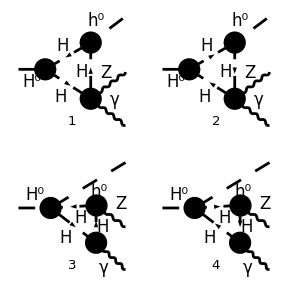

```mathematica
Paint[triangleH, Numbering->Simple, SheetHeader->None, ColumnsXRows->{2,2}];
```

```mathematica
Clear[ampsTriangle]
ampsTriangle = CreateFeynAmp[triangleH, Truncated->True, GaugeRules->{_FAGaugeXi->1} ];
ampsTriangle = FCFAConvert[ampsTriangle, IncomingMomenta->{q}, OutgoingMomenta->{k1, k2, k3},
LoopMomenta->{l}, ChangeDimension-> D, UndoChiralSplittings-> True, 
DropSumOver->True, TransversePolarizationVectors->{k1, k2}, List->True,
SMP->True, LorentzIndexNames->{μ,ν,ρ, δ, λ},  SUNIndexNames->{a,b,c,d,e,f,g,h}, SUNFIndexNames->{w, v, z, x, m, n , q, r}]/.ConventionNotation//Contract//FCTraceFactor//Simplify;
```

```mathematica
F1tr = P1[μ,ν]ampsTriangle // Contract//Expand;
F2tr = P2[μ,ν] ampsTriangle // Contract//Expand;
F3tr = P3[μ,ν] ampsTriangle // Contract//Expand;
```

```mathematica
f1trreduced =F1tr/.squareloopterms/.looplineardependences;
f2trreduced = F2tr/.squareloopterms/.looplineardependences;
f3trreduced = F3tr/.squareloopterms/.looplineardependences;
```

```mathematica
f1trres = f1trreduced//TID[#, l, ToPaVe->True]&//Simplify;
f2trres = f2trreduced// TID[#, l, ToPaVe->True]&//Simplify;
f3trres = f3trreduced// TID[#, l, ToPaVe->True]& //Simplify;
```

```mathematica
f1tr =  f1trres/.Kinematics/.InvariantKinematics
f2tr =  f2trres/.Kinematics/.InvariantKinematics
f3tr =  f3trres/.Kinematics/.InvariantKinematics
```

{(ⅈ (D-1) g_H0HH g_hHH (q_13-m_h0^2) g_(H H Z γ) C_0(m_Z^2,-m_Z^2+q_23,m_H0^2,m_Hp^2,m_Hp^2,m_Hp^2))/(32 π^2),(ⅈ (D-1) g_H0HH g_hHH (q_13-m_h0^2) g_(H H Z γ) C_0(m_Z^2,-m_Z^2+q_23,m_H0^2,m_Hp^2,m_Hp^2,m_Hp^2))/(32 π^2),1/(16 π^2 D)ⅈ g_(H H γ) g_(H H Z) g_(H H H0 h0) (2 (D-1) (q_13-m_h0^2) B_0(-m_Z^2+q_23,m_Hp^2,m_Hp^2)+(1/2 D m_h0^2 (q_12-m_Z^2)-1/2 (q_13-m_h0^2) (1/2 D (-m_h0^2-m_Z^2+q_23)-4 (D-1) m_Hp^2)) C_0(0,m_h0^2,-m_Z^2+q_23,m_Hp^2,m_Hp^2,m_Hp^2)),1/(16 π^2 D)ⅈ g_(H H γ) g_(H H Z) g_(H H H0 h0) (2 (D-1) (q_13-m_h0^2) B_0(-m_Z^2+q_23,m_Hp^2,m_Hp^2)+(1/2 D m_h0^2 (q_12-m_Z^2)-1/2 (q_13-m_h0^2) (1/2 D (-m_h0^2-m_Z^2+q_23)-4 (D-1) m_Hp^2)) C_0(0,m_h0^2,-m_Z^2+q_23,m_Hp^2,m_Hp^2,m_Hp^2))}

{(ⅈ (D-1) g_H0HH g_hHH g_(H H Z γ) (-m_h0^2-m_Z^2+q_23) C_0(m_Z^2,-m_Z^2+q_23,m_H0^2,m_Hp^2,m_Hp^2,m_Hp^2))/(32 π^2),(ⅈ (D-1) g_H0HH g_hHH g_(H H Z γ) (-m_h0^2-m_Z^2+q_23) C_0(m_Z^2,-m_Z^2+q_23,m_H0^2,m_Hp^2,m_Hp^2,m_Hp^2))/(32 π^2),1/(8 π^2 D)ⅈ (D-1) g_(H H γ) g_(H H Z) g_(H H H0 h0) (-m_h0^2-m_Z^2+q_23) (B_0(-m_Z^2+q_23,m_Hp^2,m_Hp^2)+m_Hp^2 C_0(0,m_h0^2,-m_Z^2+q_23,m_Hp^2,m_Hp^2,m_Hp^2)),1/(8 π^2 D)ⅈ (D-1) g_(H H γ) g_(H H Z) g_(H H H0 h0) (-m_h0^2-m_Z^2+q_23) (B_0(-m_Z^2+q_23,m_Hp^2,m_Hp^2)+m_Hp^2 C_0(0,m_h0^2,-m_Z^2+q_23,m_Hp^2,m_Hp^2,m_Hp^2))}

{-1/(8 π^2 (-m_h0^2-m_Z^2+q_23))ⅈ g_H0HH g_hHH g_(H H Z γ) (1/2 m_Z^2 (-m_h0^2-m_Z^2+q_23)+1/4 (q_13-m_h0^2) (q_12-m_Z^2)) C_0(m_Z^2,-m_Z^2+q_23,m_H0^2,m_Hp^2,m_Hp^2,m_Hp^2),-1/(8 π^2 (-m_h0^2-m_Z^2+q_23))ⅈ g_H0HH g_hHH g_(H H Z γ) (1/2 m_Z^2 (-m_h0^2-m_Z^2+q_23)+1/4 (q_13-m_h0^2) (q_12-m_Z^2)) C_0(m_Z^2,-m_Z^2+q_23,m_H0^2,m_Hp^2,m_Hp^2,m_Hp^2),-1/(4 π^2 D (-m_h0^2-m_Z^2+q_23))ⅈ g_(H H γ) g_(H H Z) g_(H H H0 h0) (2 (1/2 m_Z^2 (-m_h0^2-m_Z^2+q_23)+1/4 (q_13-m_h0^2) (q_12-m_Z^2)) B_0(-m_Z^2+q_23,m_Hp^2,m_Hp^2)+(1/4 (q_13-m_h0^2) (q_12-m_Z^2) (2 m_Hp^2-1/2 D (-m_h0^2-m_Z^2+q_23))+m_Hp^2 m_Z^2 (-m_h0^2-m_Z^2+q_23)) C_0(0,m_h0^2,-m_Z^2+q_23,m_Hp^2,m_Hp^2,m_Hp^2)),-1/(4 π^2 D (-m_h0^2-m_Z^2+q_23))ⅈ g_(H H γ) g_(H H Z) g_(H H H0 h0) (2 (1/2 m_Z^2 (-m_h0^2-m_Z^2+q_23)+1/4 (q_13-m_h0^2) (q_12-m_Z^2)) B_0(-m_Z^2+q_23,m_Hp^2,m_Hp^2)+(1/4 (q_13-m_h0^2) (q_12-m_Z^2) (2 m_Hp^2-1/2 D (-m_h0^2-m_Z^2+q_23))+m_Hp^2 m_Z^2 (-m_h0^2-m_Z^2+q_23)) C_0(0,m_h0^2,-m_Z^2+q_23,m_Hp^2,m_Hp^2,m_Hp^2))}

```mathematica
f1Htr = Total[f1tr]//Simplify
f2Htr = Total[f2tr]//Simplify
f3Htr = Total[f3tr]//Simplify
```

1/(16 π^2)ⅈ (1/D 2 g_(H H γ) g_(H H Z) g_(H H H0 h0) (2 (D-1) (q_13-m_h0^2) B_0(-m_Z^2+q_23,m_Hp^2,m_Hp^2)+(1/2 D m_h0^2 (q_12-m_Z^2)-1/4 (m_h0^2-q_13) (D m_h0^2+8 (D-1) m_Hp^2+D (m_Z^2-q_23))) C_0(0,m_h0^2,-m_Z^2+q_23,m_Hp^2,m_Hp^2,m_Hp^2))+(D-1) g_H0HH g_hHH (q_13-m_h0^2) g_(H H Z γ) C_0(m_Z^2,-m_Z^2+q_23,m_H0^2,m_Hp^2,m_Hp^2,m_Hp^2))

-1/(16 π^2 D)ⅈ (D-1) (m_h0^2+m_Z^2-q_23) (4 g_(H H γ) g_(H H Z) g_(H H H0 h0) B_0(-m_Z^2+q_23,m_Hp^2,m_Hp^2)+D g_H0HH g_hHH g_(H H Z γ) C_0(m_Z^2,-m_Z^2+q_23,m_H0^2,m_Hp^2,m_Hp^2,m_Hp^2)+4 m_Hp^2 g_(H H γ) g_(H H Z) g_(H H H0 h0) C_0(0,m_h0^2,-m_Z^2+q_23,m_Hp^2,m_Hp^2,m_Hp^2))

-1/(4 π^2 (-m_h0^2-m_Z^2+q_23))ⅈ (1/D 2 g_(H H γ) g_(H H Z) g_(H H H0 h0) ((1/8 (m_h0^2-q_13) (m_Z^2-q_12) (D m_h0^2+D (m_Z^2-q_23)+4 m_Hp^2)-m_Hp^2 m_Z^2 (m_h0^2+m_Z^2-q_23)) C_0(0,m_h0^2,-m_Z^2+q_23,m_Hp^2,m_Hp^2,m_Hp^2)-1/2 (m_h0^2 (m_Z^2+q_12)+(q_13-2 q_23) m_Z^2+2 m_Z^4-q_12 q_13) B_0(-m_Z^2+q_23,m_Hp^2,m_Hp^2))-1/4 g_H0HH g_hHH g_(H H Z γ) (m_h0^2 (m_Z^2+q_12)+(q_13-2 q_23) m_Z^2+2 m_Z^4-q_12 q_13) C_0(m_Z^2,-m_Z^2+q_23,m_H0^2,m_Hp^2,m_Hp^2,m_Hp^2))

```mathematica
Clear[F1tr, F2tr, F3tr, f1trreduced, f2trreduced, f3trreduced, f1trres, f2trres, f3trres, f1tr, f2tr, f3tr];
```

```mathematica
(* Boxes Higgs *)
BoxesDiagrams = DiagramExtract[diagrams, BoxesList];
BoxesWithH = DiagramSelect[BoxesDiagrams,
!FreeQ[LoopFields[##], S[5]]&];
BoxesWithFermion =  DiagramSelect[BoxesDiagrams,
!FreeQ[LoopFields[##], F[3, {3, _}]]&];
BoxesWithoutW =  DiagramSelect[BoxesDiagrams,
FreeQ[LoopFields[##], V[3]]&];
```

```mathematica
BoxesWithoutWG = DiagramSelect[BoxesWithoutW, FreeQ[LoopFields[##],  S[6]]&];
BoxesWithoutWGt = DiagramComplement[BoxesWithoutWG, BoxesWithFermion];
BoxesWithoutWGtu = DiagramSelect[BoxesWithoutWGt, FreeQ[LoopFields[##], U[_]]&];
```

```mathematica
BoxesH = BoxesWithoutWGtu;
```

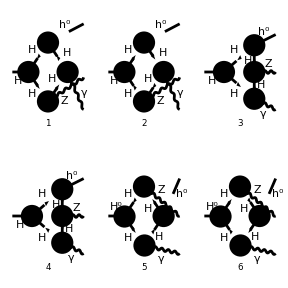

```mathematica
Paint[BoxesH, Numbering->Simple, SheetHeader->None, ColumnsXRows->{3,3}];
```

```mathematica
Clear[ampsBoxes]
ampsBoxes = CreateFeynAmp[BoxesH, Truncated->True, GaugeRules->{_FAGaugeXi->1}];
ampsBoxes = FCFAConvert[ampsBoxes, IncomingMomenta->{q}, OutgoingMomenta->{k1, k2, k3},
LoopMomenta-> {l},  ChangeDimension->D, UndoChiralSplittings->True, DropSumOver->True , TransversePolarizationVectors->{k1, k2}, List->True, 
SMP->True, LorentzIndexNames->{μ, ν, ρ, σ, δ, λ}, SUNIndexNames->{a,b,c,d,f,e,g,h},SUNFIndexNames-> {w,v,z,x,m,n,q,r}
]/.ConventionNotation//Contract//FCTraceFactor//Simplify;
```

```mathematica
F1box = P1[μ,ν] ampsBoxes // Contract // Expand;
F2box = P2[μ,ν] ampsBoxes // Contract // Expand;
F3box = P3[μ,ν] ampsBoxes // Contract // Expand;
```

```mathematica
f1boxreduced =F1box/.squareloopterms/.looplineardependences;
f2boxreduced = F2box/.squareloopterms/.looplineardependences;
f3boxreduced = F3box/.squareloopterms/.looplineardependences;
```

```mathematica
f1boxres = f1boxreduced//TID[#, l, ToPaVe->True]&//Simplify;
f2boxres = f2boxreduced// TID[#, l, ToPaVe->True]&//Simplify;
f3boxres = f3boxreduced// TID[#, l, ToPaVe->True]& //Simplify;
```

```mathematica
f1box =  f1boxres/.Kinematics/.InvariantKinematics;
f2box =  f2boxres/.Kinematics/.InvariantKinematics;
f3box =  f3boxres/.Kinematics/.InvariantKinematics;
```

```mathematica
f1Hbox = Total[f1box]//Simplify
f2Hbox = Total[f2box]//Simplify
f3Hbox = Total[f3box]//Simplify
```

1/(32 π^2 D)g_H0HH g_hHH g_(H H γ) g_(H H Z) (16 (D-1) (m_h0^2-q_13) C_0(0,m_h0^2,-m_Z^2+q_23,m_Hp^2,m_Hp^2,m_Hp^2)+8 (D-1) (m_h0^2-q_13) C_0(m_Z^2,m_h0^2,m_Z^2+q_13,m_Hp^2,m_Hp^2,m_Hp^2)-2 ((q_13-m_h0^2) (4 (D-1) m_Hp^2-1/2 D (m_h0^2+m_Z^2-q_23))-D (m_Z^2-q_12) (m_Z^2-q_23)) D_0(m_Z^2,0,m_H0^2,m_h0^2,q_12,m_Z^2+q_13,m_Hp^2,m_Hp^2,m_Hp^2,m_Hp^2)-2 ((q_13-m_h0^2) (4 (D-1) m_Hp^2-1/2 D (m_h0^2+m_Z^2-q_23))+D (q_12-m_Z^2) (-2 m_h0^2+m_Z^2+2 q_13-q_23)+D (m_h0^2-q_13)^2+4 D m_Z^2 (m_Z^2-q_23)) D_0(m_Z^2,0,m_h0^2,m_H0^2,q_12,-m_Z^2+q_23,m_Hp^2,m_Hp^2,m_Hp^2,m_Hp^2)-(-m_h0^2 (8 (D-1) m_Hp^2+D (5 m_Z^2+2 q_12+5 q_13+q_23))+3 D m_h0^4+q_13 (8 (D-1) m_Hp^2+D (-m_Z^2+2 q_13+q_23))) D_0(m_Z^2,m_h0^2,0,m_H0^2,m_Z^2+q_13,-m_Z^2+q_23,m_Hp^2,m_Hp^2,m_Hp^2,m_Hp^2))

1/(8 π^2 D)g_H0HH g_hHH g_(H H γ) g_(H H Z) (2 (D-1) (m_h0^2+m_Z^2-q_23) (C_0(m_Z^2,m_h0^2,m_Z^2+q_13,m_Hp^2,m_Hp^2,m_Hp^2)+m_Hp^2 D_0(m_Z^2,0,m_H0^2,m_h0^2,q_12,m_Z^2+q_13,m_Hp^2,m_Hp^2,m_Hp^2,m_Hp^2))+4 (D-1) (m_h0^2+m_Z^2-q_23) C_0(0,m_h0^2,-m_Z^2+q_23,m_Hp^2,m_Hp^2,m_Hp^2)+(2 m_h0^2 ((D-1) m_Hp^2+D m_Z^2)+2 (D-1) m_Hp^2 (m_Z^2-q_23)+D ((q_12-q_13-q_23) m_Z^2+m_Z^4+q_12 (q_13-q_23))) D_0(m_Z^2,0,m_h0^2,m_H0^2,q_12,-m_Z^2+q_23,m_Hp^2,m_Hp^2,m_Hp^2,m_Hp^2)+((m_h0^2+m_Z^2-q_23) (-D m_h0^2+2 (D-1) m_Hp^2+D (2 m_Z^2+q_13))-D (m_h0^2+q_13) (m_Z^2-q_12)) D_0(m_Z^2,m_h0^2,0,m_H0^2,m_Z^2+q_13,-m_Z^2+q_23,m_Hp^2,m_Hp^2,m_Hp^2,m_Hp^2))

-1/(16 D π^2 (m_h0^2+m_Z^2-q_23))g_H0HH g_hHH g_(H H Z) g_(H H γ) (-4 C_0(m_Z^2,m_h0^2,m_Z^2+q_13,m_Hp^2,m_Hp^2,m_Hp^2) (2 m_Z^4+(q_13-2 q_23) m_Z^2+m_h0^2 (m_Z^2+q_12)-q_12 q_13)+8 C_0(0,m_h0^2,-m_Z^2+q_23,m_Hp^2,m_Hp^2,m_Hp^2) ((m_Z^2-q_12) (m_h0^2-q_13)-2 m_Z^2 (m_h0^2+m_Z^2-q_23))+D_0(m_Z^2,0,m_H0^2,m_h0^2,q_12,m_Z^2+q_13,m_Hp^2,m_Hp^2,m_Hp^2,m_Hp^2) (-8 m_Hp^2 (m_h0^2+m_Z^2-q_23) m_Z^2+(q_12-m_Z^2) ((m_h0^2-q_13) (D m_h0^2-4 m_Hp^2+D (m_Z^2-q_23))-2 D m_Z^2 (m_h0^2+m_Z^2-q_23))-D (m_Z^2-q_12)^2 (2 m_h0^2+m_Z^2-q_13-q_23))+D_0(m_Z^2,0,m_h0^2,m_H0^2,q_12,-m_Z^2+q_23,m_Hp^2,m_Hp^2,m_Hp^2,m_Hp^2) (D (3 m_Z^2+q_12) m_h0^4-(4 m_Hp^2 (m_Z^2+q_12)-D (3 m_Z^2+q_12) (m_Z^2-2 q_12-q_13-q_23)) m_h0^2+m_Hp^2 (-8 m_Z^4-4 (q_13-2 q_23) m_Z^2+4 q_12 q_13)-D (3 m_Z^2+q_12) (m_Z^4+(q_12+2 q_13-q_23) m_Z^2-q_13 q_23-q_12 (q_13+q_23)))-D_0(m_Z^2,m_h0^2,0,m_H0^2,m_Z^2+q_13,-m_Z^2+q_23,m_Hp^2,m_Hp^2,m_Hp^2,m_Hp^2) (2 D m_h0^6-D (3 m_Z^2+3 q_12+4 q_13+2 q_23) m_h0^4+(4 (m_Z^2+q_12) m_Hp^2+D (-4 m_Z^4+(3 q_12-q_13+7 q_23) m_Z^2+q_12^2+q_12 (5 q_13+q_23)+2 q_13 (q_13+2 q_23))) m_h0^2+4 m_Hp^2 (2 m_Z^4+(q_13-2 q_23) m_Z^2-q_12 q_13)+D (3 m_Z^2+q_12+2 q_13) (2 m_Z^4+2 (q_13-q_23) m_Z^2-q_13 (q_12+q_23))))

```mathematica
Clear[F1box, F2box, F3box, f1boxreduced, f2boxreduced, f3boxreduced, f1boxres, f2boxres, f3boxres, f1box, f2box, f3box];
```

```mathematica
f1H = f1Hself + f1Htr + f1Hbox//Simplify;
f2H = f2Hself + f2Htr + f2Hbox//Simplify;
f3H = f3Hself + f3Htr + f3Hbox//Simplify;
```

```mathematica
PaVeUVPart[f1H]/.D->4 - 2ϵ//Series[#, {ϵ, 0, -1}]&
PaVeUVPart[f2H]/.D->4 - 2ϵ//Series[#, {ϵ, 0, -1}]&
PaVeUVPart[f3H]/.D->4 - 2ϵ//Series[#, {ϵ, 0, -1}]&
```

-(3 ((m_h0^2-q_13) g_(H H H0 h0) (4 g_(H H Z γ)+8 ⅈ g_(H H γ) g_(H H Z))))/(128 π^2 ϵ)+O(ϵ^0)

-(3 (g_(H H H0 h0) (g_(H H Z γ)+2 ⅈ g_(H H γ) g_(H H Z)) (m_h0^2+m_Z^2-q_23)))/(32 π^2 ϵ)+O(ϵ^0)

-(g_(H H H0 h0) (g_(H H Z γ)+2 ⅈ g_(H H γ) g_(H H Z)) (q_12 m_h0^2+m_h0^2 m_Z^2+q_13 m_Z^2-2 q_23 m_Z^2+2 m_Z^4-q_12 q_13))/(32 ϵ (π^2 (m_h0^2+m_Z^2-q_23)))+O(ϵ^0)